```mathematica
dir=NotebookDirectory[];
files=FileNames["dut*.dat",dir]
comments=Import[ParentDirectory[dir]<>"\\comments.txt","table","FieldSeparators"->"\t"]
```

{C:\Users\rfrazier\python-workspace\adpd5000_multidut_characterization\log\Generic Test_20191219_175514\data\dut0.dat}

{}

```mathematica
file=files[[1]];
decimate[x_,n_]:=Mean@Transpose[Partition[x,n]];
dat=N@Transpose[Import[file,"Table","FieldSeparators"->"\t"][[3;;-100]]];

{
time,
sltA1,
sltA2,
sltB1,
sltB2,
sltC1,
sltC2,
sltD1,
sltD2
}=dat[[1;;]];
swapA=(√((sltA1*sltB2)/(sltA2*sltB1)))^-1;
swapB=(√((sltC1*sltD2)/(sltC2*sltD1)))^-1;
```

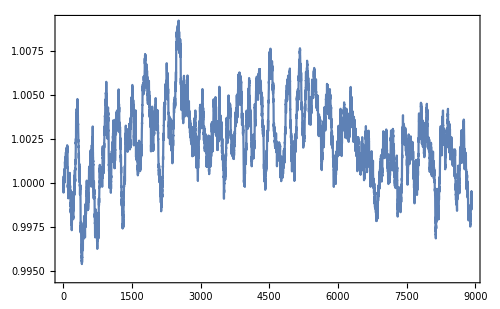

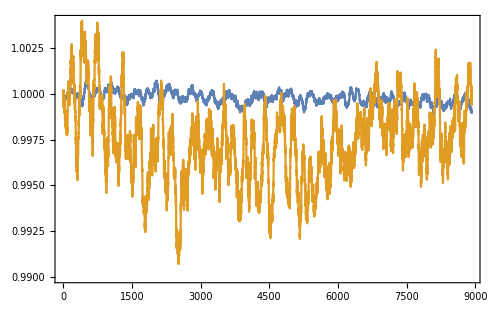

```mathematica
ListLinePlot[MovingAverage[#/Mean[#[[1;;1000]]],100]&/@{swapA/swapB},plotOptions]
ListLinePlot[MovingAverage[#/Mean[#[[1;;1000]]],100]&/@{swapA,swapB},plotOptions]
```

Look at config file for slot descriptions

```mathematica
10^(-50./20)
```

0.00316228

### Testing Drift Cancellation Algorithm

```mathematica
decimation=10;
A0=ch0[[1]]^-1;
A1=ch1[[1]]^-1;
tDec=decimate[time,decimation];
ch0=decimate[√(sltG1*sltH2),decimation];
ch1=decimate[√(sltG2*sltH1),decimation];
(*ch0=decimate[√(sltI1*sltJ2),decimation];
ch1=decimate[√(sltI2*sltJ1),decimation];*)
ratio=ch1/ch0;
(*ListLinePlot[{ch0/ch0[[60]][[1;;2000]],ch1/ch1[[60]][[1;;2000]]},plotOptions]
ListLinePlot[ratio[[1;;2000]]/ratio[[60]],plotOptions,PlotMarkers->Automatic]*)
```

```mathematica
Export[NotebookDirectory[]<>"decimatedData.dat",Transpose[{tDec,ch0,ch1}]]
```

C:\Users\rfrazier\python-workspace\adpd5000_multidut_characterization\log\TempSweep_WithButane_20191119_111458\data\decimatedData.dat

```mathematica
Mean[#]/StandardDeviation[#]&[ratio[[1;;100]]]
```

2342.44

#### Tracking how channel Ratios shift

```mathematica
A0=ch0[[1]]^-1;
A1=ch1[[1]]^-1;
ratioThreshold=10^(-50/20.) (*ratio threshold set to 50dB*)
validResponseRatio=3.3;
validResponseSpread=0.2;
Table[
rr=(A0 ch0[[j]])/(A1 ch1[[j]]);
If[Abs[rr-1]≥ratioThreshold,
(*Ratio Shifted*)
,
(*No Ratio Shift*)
0]
,{j,Length[ratio]}]
```

0.00316228

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Null,0,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,0,0,0,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,0,0,0,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,0,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

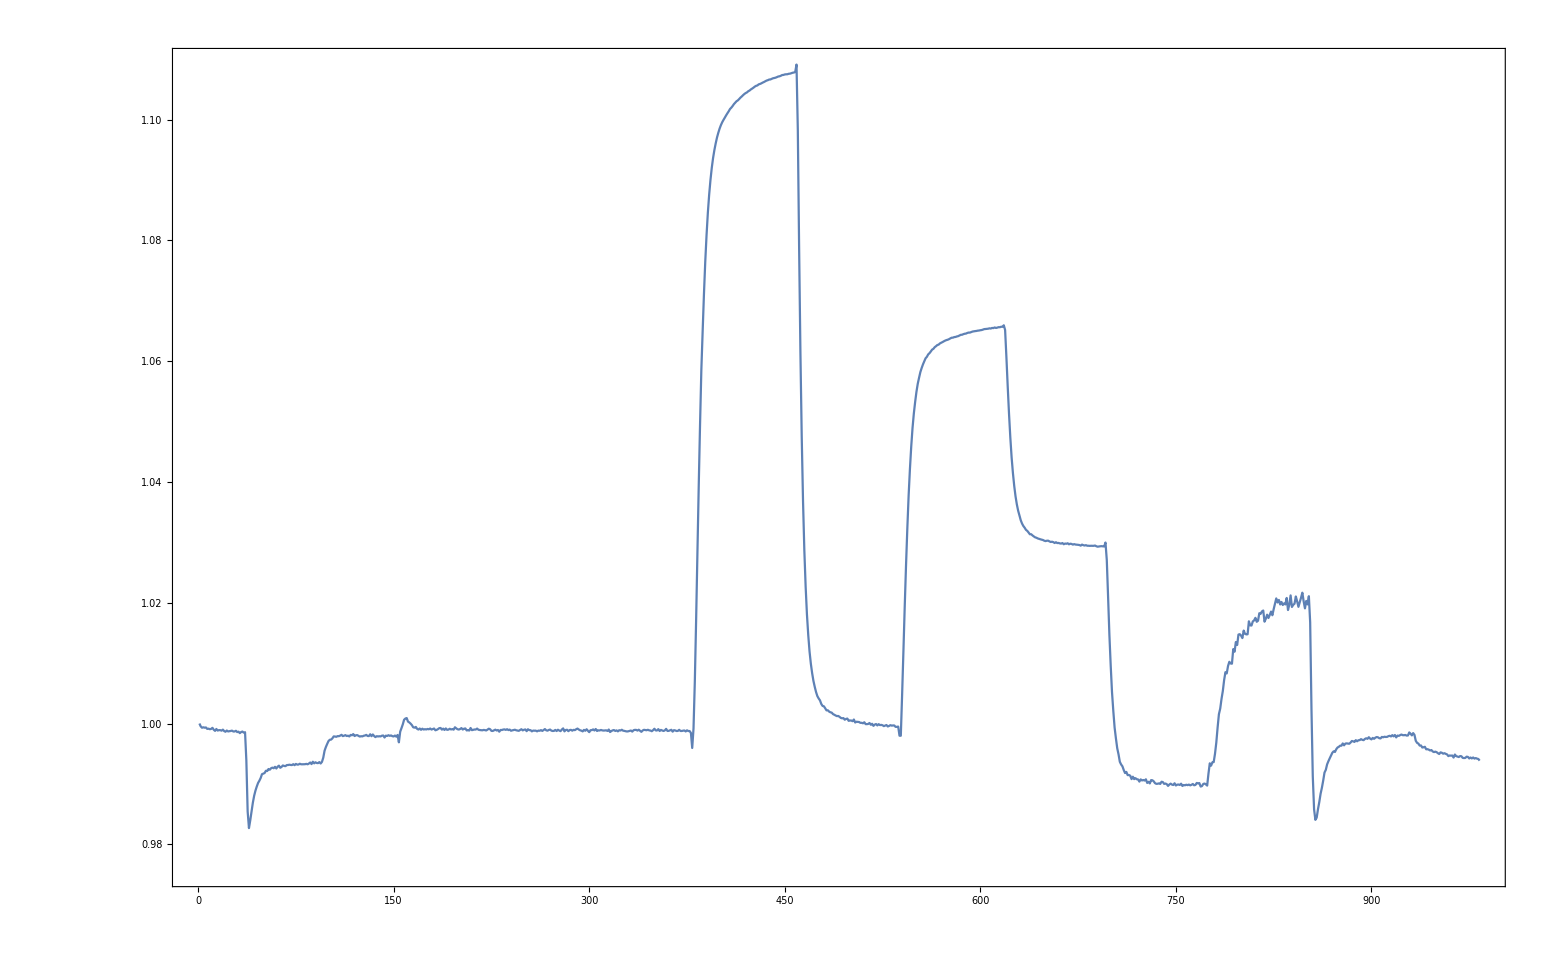

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

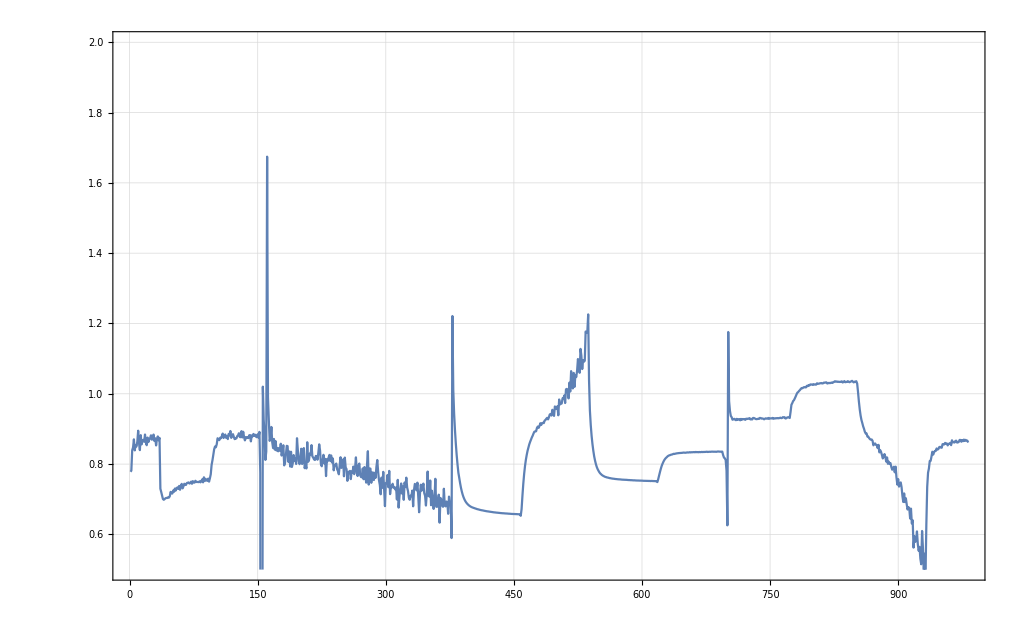

```mathematica
ListLinePlot[(A1 ch1)/(A0 ch0),plotOptions]

ListLinePlot[{((1-A0 ch0)/(1-A1 ch1))[[2;;]]},PlotRange->{.5,2},plotOptions,GridLines->Automatic]
```

```mathematica
a=(0.9912-0.9760)/0.9912
b=(0.9925-0.9805)/0.9805
```

0.0153349

0.0122387

1.25299

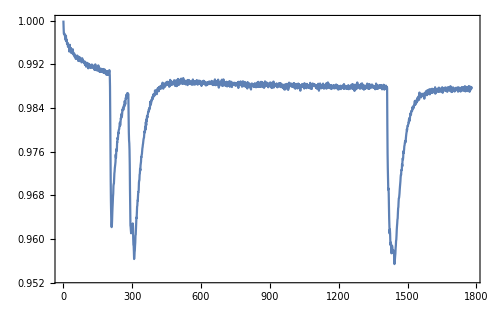

```mathematica
a/b
```

#### Algorithm Implementation

```mathematica
decimation=100;

(*ListLinePlot[ch1/ch0,PlotRange->All]*)
ratioThreshold=10^(-50/20.) (*ratio threshold set to 50dB*)
validResponseRatio=3.3;
validResponseSpread=0.2;
A0=ch0[[1]]^-1;
A1=ch1[[1]]^-1;
Table[
ratio=(A1 ch1[[j]])/(A0 ch0[[j]]);
If[Abs[1-ratio]≥ratioThreshold,
tmp=Log[A1 ch1[[j]]]/Log[A0 ch0[[j]]];
(*If[Abs[tmp-validResponseRatio]≤validResponseSpread,
1-ratio,
0
];*)
A0=ch0[[j]]^-1;
A1=ch1[[j]]^-1;
tmp
,0
]
,{j,Length[ch0]}]
```

0.00316228

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.23709,1.58181,0,0,1.24899,0,0,1.57538,0,1.42085,0,0,0,0,1.3633,0,0,1.59601,0,0,0,0,0,0,1.75029,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.27933,1.7138,0,0,0,0,1.32303,0,0,1.51824,0,0,0,1.80093,0,0,0,0,0,0}

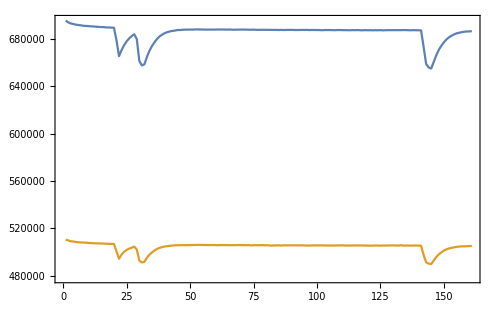

```mathematica
ListLinePlot[#[[1;;]]&/@{ch1,ch0},plotOptions]
```

```mathematica
ch0[[1]]
```

505449.

### Analyzing Dark Signals

```mathematica
decimation=100;
Row[{
ListLinePlot[XYArray[decimate[(time-time[[1]])/60,decimation],decimate[#,decimation]]&/@{sltE1,sltE2,sltF1,sltF2},plotOptions,GridLines->Automatic,PlotLabel->"8 Pulses"],
ListLinePlot[XYArray[decimate[(time-time[[1]])/60,decimation],decimate[#,decimation]]&/@{sltK1,sltK2,sltL1,sltL2},plotOptions,GridLines->Automatic,PlotLabel->"128 Pulses"]
}]
```

ListLinePlot::nonopt: Options expected (instead of plotOptions) beyond position 1 in ListLinePlot[«1»]. An option must be a rule or a list of rules.

General::stop: Further output of ListLinePlot::nonopt will be suppressed during this calculation.

ListLinePlot[1]ListLinePlot[{1},plotOptions,GridLines→Automatic,PlotLabel→128 Pulses]
 |  |  |  |

#### RMS Amplitude of Dark Codes

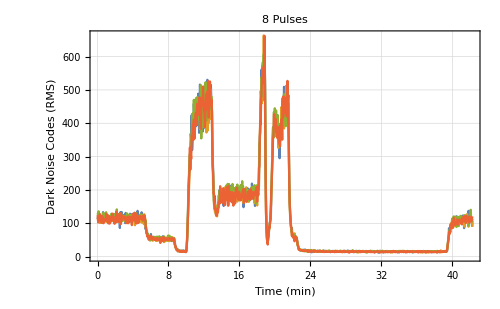
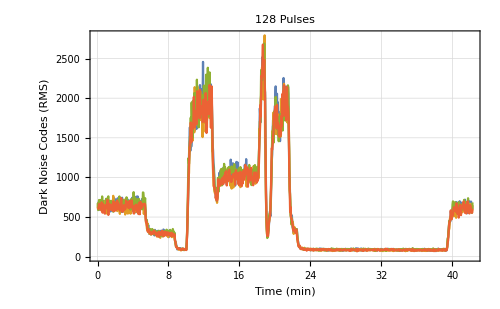

```mathematica
decimation=100;
Row[{
ListLinePlot[
Table[
XYArray[decimate[(time-time[[1]])/60,decimation],√Mean[(#-Mean[#])^2]&/@Partition[slot,decimation]]
,{slot,{sltE1,sltE2,sltF1,sltF2}}]
,plotOptions,GridLines->Automatic,FrameLabel->{"Time (min)","Dark Noise Codes (RMS)"},PlotLabel->"8 Pulses"],
ListLinePlot[
Table[
XYArray[decimate[(time-time[[1]])/60,decimation],√Mean[(#-Mean[#])^2]&/@Partition[slot,decimation]]
,{slot,{sltK1,sltK2,sltL1,sltL2}}]
,plotOptions,GridLines->Automatic,FrameLabel->{"Time (min)","Dark Noise Codes (RMS)"},PlotLabel->"128 Pulses"]
}]
```

### Tracking SNR Ch1 vs. Ch2

```mathematica
decimation=100;
Row[{
ListLinePlot[
Table[
XYArray[decimate[(time-time[[1]])/60,decimation],√Mean[(#-Mean[#])^2]&/@Partition[slot,decimation]]
,{slot,{sltE1,sltE2,sltF1,sltF2}}]
,plotOptions,GridLines->Automatic,FrameLabel->{"Time (min)","Dark Noise Codes (RMS)"},PlotLabel->"8 Pulses"],
ListLinePlot[
Table[
XYArray[decimate[(time-time[[1]])/60,decimation],√Mean[(#-Mean[#])^2]&/@Partition[slot,decimation]]
,{slot,{sltK1,sltK2,sltL1,sltL2}}]
,plotOptions,GridLines->Automatic,FrameLabel->{"Time (min)","Dark Noise Codes (RMS)"},PlotLabel->"128 Pulses"]
}]
```

### Looking at swap data for 4 pulses vs 128 pulses

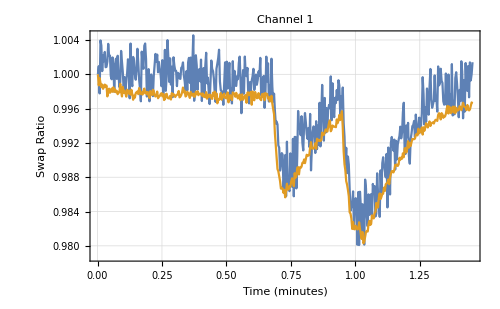
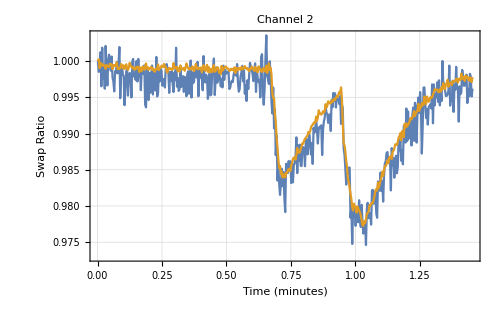

```mathematica
decimation=10;
Row[{
ListLinePlot[XYArray[decimate[(time-time[[1]])/60,decimation],decimate[#/Mean[#[[1;;decimation]]],decimation]]&/@{swap4Pulses,swap128Pulses},plotOptions,GridLines->Automatic,FrameLabel->{"Time (minutes)","Swap Ratio"},PlotLabel->"Channel 1"],
ListLinePlot[XYArray[decimate[(time-time[[1]])/60,decimation],decimate[#/Mean[#[[1;;decimation]]],decimation]]&/@{swap4PulsesCh2,swap128PulsesCh2},plotOptions,GridLines->Automatic,FrameLabel->{"Time (minutes)","Swap Ratio"},PlotLabel->"Channel 2"]
}]
```